#### One Lane Road

```mathematica
Clear["Global`*"]

dNeedToCover=width+length;
distanceBetweenCars=x;
vCarNotMe=vb;
vCarMe=va;

timeVaToCross=dNeedToCover/vCarMe;

distanceVbCovers=vCarNotMe*timeVaToCross;
bufferZone=distanceBetweenCars-distanceVbCovers-width;

probabilityOfNotHittingCar==Expand[bufferZone/(length+distanceBetweenCars)]
```

probabilityOfNotHittingCar==-(length vb)/(va (length+x))-width/(length+x)-(vb width)/(va (length+x))+x/(length+x)

#### Two Lane Road

```mathematica
Clear["Global`*"]

laneSpace=width/2;
dNeedToCoverC=2width+length+laneSpace;
dNeedToCoverB=width+length;
distanceBetweenCars=x;
vCarNotMeB=vb;
vCarNotMeC=vc;
vCarMe=va;

timeVaToCrossC=dNeedToCoverC/vCarMe;
timeVaToCrossB=dNeedToCoverB/vCarMe;

distanceVbCovers=vCarNotMeB*timeVaToCrossB;
distanceVcCovers=vCarNotMeC*timeVaToCrossC;
bufferZone=distanceBetweenCars-distanceVbCovers-distanceVcCovers-width;

probabilityOfNotHittingCar==Expand[bufferZone/(length+distanceBetweenCars)]
```

probabilityOfNotHittingCar==-(length vb)/(va (length+x))-(length vc)/(va (length+x))-width/(length+x)-(vb width)/(va (length+x))-(5 vc width)/(2 va (length+x))+x/(length+x)

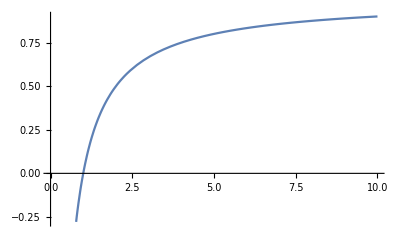

```mathematica
Plot[1-1/va,{va,0,10}]
```